### Definition

```mathematica
a=Rationalize@1;
δa[r_]=(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3);α=Rationalize@0.01;u0=10^-20;δstart=10^-10;m=100;αSch=2m;ee={10^-10,10^-5,0.001,0.003,0.007,0.01,0.03,0.07,0.1,0.3,0.7,1};
Vs1[r_,a_,c1_]=- α/r Erf[r/(√2 a)]+c1 a^2 δa[r];
Vs2[r_,a_,{c2_,d1_}]=- α/# Erf[#/(√2 a)]-2π α c2 a^2 δa[#]+(π α)/2 d1 a^4(-(3 ⅇ^(-#^2/(2 a^2)))/(2 √2 a^5 π^(3/2))+(ⅇ^(-#^2/(2 a^2)) #^2)/(2 √2 a^7 π^(3/2)))&[r];V[r_]=-α/r;
```

```mathematica
RB[n_,r_]=2/(A^(3/2) n^(3/2)) ⅇ^(-r/(n A)) Hypergeometric1F1[1-n,2,(2 r)/(n A)]/.A->Rationalize@(1/(m α));
RS[e_,r_]=2 √(2 m e)ⅇ^(π/(2 √(2m e)))Gamma[1-I/(√(2m e))] ⅇ^(-I √(2m e)r)Hypergeometric1F1[I/(√(2m e))+1,2,2I √(2m e)r];
```

```mathematica
RealEigenEnergy[n_]=-(m α^2)/(2 n^2);
Table20REE=Table[RealEigenEnergy[n],{n,20}]
```

{-1/200,-1/800,-1/1800,-1/3200,-1/5000,-1/7200,-1/9800,-1/12800,-1/16200,-1/20000,-1/24200,-1/28800,-1/33800,-1/39200,-1/45000,-1/51200,-1/57800,-1/64800,-1/72200,-1/80000}

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
EigenEnergy[V_,αSch_,{min_,max_},{opt1___},{opt2___}]:=
Module[{ef,evShifted},
PrintTemporary[V];
Module[{shift=10,d=2000,n=20,ev},{ev,ef}=NDEigensystem[{shift f[r]+V f[r]-1/αSch f''[r](*+NeumannValue[0,r==d]*),DirichletCondition[f[r]==0,True]},f[r],{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.1}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evShifted=ev-shift];
Print[evShifted];
Table[
PrintTemporary[n];
Module[{sol,evnew,steps=∞,time1,time2},
sol=ParametricNDSolve[{V u[r]-1/αSch u''[r]==e u[r],u'[max]==-min,u[max]==min},u,{r,min,max},e,MaxSteps->steps,opt1];
evnew=e/.
FindRoot[u[e][min]==0/.sol,If[n<5,{e,SetPrecision[0.99#[[n]],6],SetPrecision[1.01#[[n]],6]}&[evShifted],{e,SetPrecision[0.99#[[n]],6],SetPrecision[1.01#[[n]],6]}&[Table20REE]],opt2(*,StepMonitor:>PrintTemporary[e]*)]],{n,20}]
]
δ50e[en_,V_]:=Module[{sol,δs,δr,r1=50,r2=u0,β,jder,nder,k,wpc=50,prc=20,time1,time2},
time1=SessionTime[];
k=√(2en);
β:=r1 u'[r1]/u[r1]-1;
jder[r_]=D[SphericalBesselJ[0,r],r];
nder[r_]=D[SphericalBesselY[0,r],r];sol=Flatten@NDSolve[{u''[r]+αSch(en-V)u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},PrecisionGoal->prc,WorkingPrecision->wpc, MaxSteps->Infinity,InterpolationOrder->All(*,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}*)(*,SolveDelayed->True*)];
δs=FindRoot[(*u'[r1]/u[r1]==k Cot[k r1+δ]*)Tan[δ]==(k r1 jder[k r1]-β SphericalBesselJ[0,k r1])/(k r1 nder[k r1]-β SphericalBesselY[0,k r1])(*u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]*)/.sol,{δ,0},WorkingPrecision->wpc,PrecisionGoal->prc];
δr=δ/.δs;
time2=SessionTime[];
(*PrintTemporary["End with "<>ToString[time2-time1]<>"s"];*)
δr=NestWhile[Sign[#](Abs[#]-π)&,δr,Abs[#]>π/2&]
]
δ50[V_]:=Module[{en,len,δen,timestampa,timestampb},
len=Length@ee;
ParallelTable[
timestampa=SessionTime[];
en=ee[[i]];
δen=δ50e[en,V];
timestampb=SessionTime[];
PrintTemporary[{en,δen},"    ",timestampb-timestampa];
δen,{i,2,len}]
]
Eigenfun[V_,enelist_]:=Module[{},Flatten[With[{r1=2000,r2=1.*10^-50},NDSolve[{V f[r]-1/αSch f''[r]==# f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},WorkingPrecision->50,AccuracyGoal->30,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepSize->0.01,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}]]&/@enelist,2]]
```

```mathematica
Eigenfunsin[V_,ene_,rr_,{r1_,r2_},opt___]:=
Module[{efunction,amplitude},efunction=Flatten[NDSolve[{V f[r]-1/αSch f''[r]==ene f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},opt,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}],2];
amplitude=NIntegrate[f[r]^2/.#,{r,r2,r1}]^-0.5&/@efunction;
amplitude f[rr]/.efunction
]
```

```mathematica
EigenEnergySolo[V_,αSch_,{min_,max_},{estart_,eend___},{opt1___},{opt2___}]:=
Module[{sol,ef,evShifted,evnew,steps=∞,time1,time2},
PrintTemporary[V];
sol=ParametricNDSolve[{V u[r]-1/αSch u''[r]==e u[r],u[max]==min,u'[max]==-min},u,{r,min,max},e,MaxSteps->steps,(*StepMonitor:>PrintTemporary[{r,u[e][r]}],*)opt1];
PrintTemporary[{estart,eend}];
time2=SessionTime[];
evnew=e/.#&/@
FindRoot[u[e][min]==0/.sol,{e,estart,eend},opt2,StepMonitor:>{time1=time2;time2=SessionTime[];Print[{e,u[e][min]/.sol},"time:",time2-time1,"s"]}]]
```

```mathematica
δexpminus10=δ50e[10^-10,V[r]];
δexpminus9=δ50e[10^-9,V[r]];
δexpminus5=δ50e[10^-5,V[r]];
(*δ50V=δ50[V[r]]*)
```

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.000678812640161460376815013380166025427816629657566) 小于 WorkingPrecision (50.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.00214659338689587066523596213673381433488768031093) 小于 WorkingPrecision (50.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.213592724017438896075009561055777584774782250946) 小于 WorkingPrecision (50.).

```mathematica
(*Get["C:\\Users\\ASUS\\Documents\\Coulomb_psir_comparasion2.mx"]*)
```

### Determine c_1

```mathematica
hhhc1[en_,c1_?NumberQ]:=δ50e[en,Vs1[r,a,c1]];
evnhhhc1[c1_]:=N[hhhc1[10^-10,c1]-δexpminus10,8];
Determinec1[{start_,end___},opt___]:=Module[{aaa,findroot,mon},aaa=a;
Print[aaa];
Monitor[findroot=FindRoot[hhhc1[10^-10,c1]==δexpminus10,{c1,start,end},opt,StepMonitor:>{mon={c1,evnhhhc1[c1]}}],mon];
Print[c1/.findroot];
c1/.findroot
]
```

```mathematica
c1=Determinec1[{-0,-1},{MaxIterations->200,AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->50}]
```

0.1

NDSolve::precw: The precision of the differential equation ({{20 (1.×10^-10+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000682475643443809801038864984663202512734798605464) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (1/10000000000+0.634936 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000676980199376761675928131128901388010769670272257) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (1/10000000000+0.634936 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000676980199376761675928131128901388010769670272257) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

-0.69202747389763147323087738870043965968435665340985

-0.69202747389763147323087738870043965968435665340985

#### Vs_1’s eigensystem

```mathematica
energyVs1=EigenEnergy[Vs1[r,a,c1],αSch,{10^-15,Which[n<10,1000,11≤n<15,1800,15≤n<19,3000,n≥19,4000]},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}];
N[%,6]
```

ParametricNDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) u[r$6977]-u''[r$6977]/20==e$6976 u[r$6977],u'[Which[n<10,1000,11≤n<15,1800,15≤n<19,3000,n≥19,4000]]==-1/1000000000000000,u[Which[n<10,1000,11≤n<15,1800,15≤n<19,3000,n≥19,4000]]==1/1000000000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

General::stop: Further output of FindRoot::brdig will be suppressed during this calculation.

{-0.0500079,-0.0125002,-0.00555559,-0.00312501,-0.002,-0.00138889,-0.00102041,-0.00078125,-0.000617284,-0.0005,-0.000413223,-0.000347222,-0.000295858,-0.000255102,-0.000222222,-0.000195313,-0.000173011,-0.000154327,-0.000138443,-0.000124049}

```mathematica
efVs1=Module[{efunction=Range@20},
SetSharedVariable[efunction];
ParallelTable[
efunction[[n]]=First@Eigenfunsin[Vs1[r,a,c1],energyVs1[[n]],r,{If[n>15,4000,2000],1.*10^-50},WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4];
efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]],{n,1,20}];
efunction
];
```

LinkOpen::linke: Unknown MathLink problem encountered..

General::stop: Further output of LinkOpen::linke will be suppressed during this calculation.

SubKernels`RemoteKernels`LaunchRemote::somefail: 4 of 4 kernels failed to launch.

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.0500078698243857713717887787042 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.00555558766918011422453272884499 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.0020000024955053743545081067507 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.00102040862718159308255476878961 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000617284082651037425612626405505 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000500000077962926767212370479046 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000413223188903938764724442381674 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000347222253552894468125638263566 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

$Aborted

#### ψ_r Vs_1

```mathematica
IntegrationVs11st=NIntegrate[efVs1[[#]]/(√(4π)r)δa[r] r^2,{r,0,2000},MaxRecursion->20,WorkingPrecision->30,AccuracyGoal->10]&/@Range@20;
```

```mathematica
ψrTrueVs1[n_][γ_,η_]:=4π(γ Integration1st[[n]])
```

```mathematica
DetermineVs1[r0_]:=Module[{REAL,REF,RES,ψr,ERROR,REFRANGE={20}},
(*Print[r0];*)
(*REAL=NLimit[efV[[#]]/(√(4π)r),r->r0,WorkingPrecision->30]&/@Range@20;*)
REF=Limit[RS[n,r]/(√(4π)),r->r0]&/@REFRANGE;
RES=FindRoot[Thread[ψrTrueVs1[#][γ,η]&/@REFRANGE==REF],{γ,0,1},AccuracyGoal->10,MaxIterations->200,WorkingPrecision->30];
(*ψr=ψrTrue[#][γ,η]/.RES&/@Range@20;
ERROR=Abs[(ψr-REAL)/REAL];*)
(*Print[N[ERROR,6]];*)
{r0,γ}(*,N[ERROR,6]*)/.RES
]
```

```mathematica
Determine[0]
```

```mathematica
Module[{γη},
γlVs1={};
Monitor[Table[
γη=Determine[r0];
AppendTo[γlVs1,γη];
,{r0,0,1,0.001}],Row[{ProgressIndicator[r0,{0,1}],100 r0/1"%"}]]];
```

```mathematica
γrVs1=Interpolation[γlVs1]
```

```mathematica
ψrfunVs1[r_][n_]:=4π(γrVs1[r] IntegrationVs11st[[n]])
```

```mathematica
GraphicsGrid@{{Plot[γrVs1[r],{r,0,1},ImageSize->Medium,PlotStyle->Orange,PlotLabel->"γ̃"]}}
GraphicsGrid@Partition[Table[Plot[{ψrfunVs1[r][n],RS[n,r]/(√(4π))},{r,0,1},PlotStyle->{{},{Dashed}},ImageSize->230],{n,1,20}],5]
```

### Determine c_2 & d_1

```mathematica
hhh[en_,c2_?NumberQ,d1_?NumberQ]:=δ50e[en,Vs2[r,a,{c2,d1}]]
evnhhh1:=N[hhh[ee[[1]],c2,d1]-δexpminus10,8];
evnhhh2:=N[hhh[10^-9,c2,d1]-δexpminus9,8];
```

```mathematica
Determinec2d1[{c2start_,c2end___},{d1start_,d1end___}]:=Module[{findroot,mon},
Monitor[findroot=FindRoot[{hhh[ee[[1]],c2,d1]==δexpminus10,hhh[10^-9,c2,d1]==δexpminus9},{{c2,c2start,c2end},{d1,d1start,d1end}},MaxIterations->100,AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->50,StepMonitor:>{mon={c2,d1,evnhhh1,evnhhh2};If[evnhhh1<10^-7&&evnhhh2<10^-7,Print@mon]}],mon];
{c2,d1}/.findroot
]
```

```mathematica
{c2,d1}=Determinec2d1[{2.1,2},{1,2}]
```

NDSolve::precw: 微分方程的精度 ({{200 (1/10000000000+0.00837779 Power[«2»]-0.015708 Plus[«2»]+1/100 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.000682815280608624794707284893820203686242734162864) 小于 WorkingPrecision (50.).

NDSolve::precw: 微分方程的精度 ({{200 (1/1000000000+0.00837779 Power[«2»]-0.015708 Plus[«2»]+1/100 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.00215925100961133095245266784463730296737707660722) 小于 WorkingPrecision (50.).

NDSolve::precw: 微分方程的精度 ({{200 (1/10000000000+0.00797885 Power[«2»]-0.015708 Plus[«2»]+1/100 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.000684905184711160698442822116776220201958063013775) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，FindRoot::precw 的进一步输出将被抑制.

{2.07095,1.46119,2.6637931×10^-8,8.423186×10^-8}

{-4.8031113469337631531743394133223968820107929541805,15.780184647878302572037560479282969199047315606162,-7.4538726×10^-6,-0.000023571407}

{2.0398913880356028986199180065416386805459762832969,1.5231492959887964149232073770852599809652821531105,-4.1100036×10^-10,-1.3051807×10^-9}

{7.1307160812120589189356344212207644592490965137268,-9.6015525474582227927275922818018963870158588307653,-2.825314×10^-6,-8.934508×10^-6}

{1.8667783952866618590209537967359798820419687465583,1.8547144928053127064584360946877709574583817442249,-2.8465057×10^-7,-9.0015791×10^-7}

{1.7939840270468363517754926579061596373236059420883,1.9753077265171797399013463823109198326934227995849,-5.8688847×10^-7,-1.8559266×10^-6}

{1.7962875663788449065142978210683220864930688064696,1.9806734637194676536155217329576515187620172652325,-4.8750159×10^-7,-1.5416349×10^-6}

{1.8007624878161448978002857246360237686922587117083,1.9727039260380614187121186731255156104378398456807,-4.744096×10^-7,-1.5002341×10^-6}

{1.8013060437105539881714026624059440488269682275487,1.9715620575104532831151442064905764470224082737582,-4.7452012×10^-7,-1.5005836×10^-6}

{1.8013015848866188776223722216745321094192206235884,1.9715451166414904893010782480080346441715385107017,-4.7477668×10^-7,-1.5013949×10^-6}

{1.8012921686358106904373733499353784370003848900185,1.9715618492267177959323930644218167731735818470003,-4.748046×10^-7,-1.5014832×10^-6}

{1.8012911573101563981837142251116245074946033797576,1.9715640546563274361011221246770234235440670335562,-4.748036×10^-7,-1.50148×10^-6}

{1.8012911954819435485686908564552271776867057452616,1.9715640338245151260505721014257155600881129389785,-4.7480303×10^-7,-1.5014782×10^-6}

{1.8012912164808163399483256921319130012150771166231,1.9715639952174145891626084415900432518270215214325,-4.7480298×10^-7,-1.501478×10^-6}

{1.801291218272370366629650781669543474614972314629,1.9715639911135254540767606219655904851303918128235,-4.7480298×10^-7,-1.501478×10^-6}

{1.8012912181339427990601057956156033113869815607974,1.971563991274734282310941780539157138505902315042,-4.7480298×10^-7,-1.5014781×10^-6}

{1.8012912180885841886534928964638064907077011953069,1.9715639913606821670400496407571517851172812030151,-4.7480298×10^-7,-1.5014781×10^-6}

{1.8012912180856303934811711187626885172918934447249,1.9715639913679389411982303669439710797822245863513,-4.7480298×10^-7,-1.5014781×10^-6}

{1.8012912180860347691135604430529213070716534370388,1.9715639913673639601105330640886295250278947421768,-4.7480298×10^-7,-1.5014781×10^-6}

{1.8012912180861262741638237892893831761062373614289,1.9715639913671853027404032393833061284063100830388,-4.7480298×10^-7,-1.5014781×10^-6}

{1.8012912180861304741506191560212379592081539426181,1.971563991367173734085153014363811780798479254034,-4.7480298×10^-7,-1.5014781×10^-6}

{1.8012912180861294460732870234589747632722863308078,1.971563991367175347498737652163623432067807410661,-4.7480298×10^-7,-1.5014781×10^-6}

{1.8012912180861292578447540215668484789623354342042,1.9715639913671757250010607372187338173516422524518,-4.7480298×10^-7,-1.5014781×10^-6}

{1.8012912180861292530316416352845185064603181920567,1.9715639913671757420522384398062661621244102919947,-4.7480298×10^-7,-1.5014781×10^-6}

{1.8012912180861292555804644672312843119453226703786,1.9715639913671757377962806372581612561199270522492,-4.7480298×10^-7,-1.5014781×10^-6}

{1.8012912180861292559547301584870285862650362375652,1.9715639913671757370226119468036678652414005278106,-4.7480298×10^-7,-1.5014781×10^-6}

{1.801291218086129255955972583467074041523067512914,1.9715639913671757370033320095627242838016704885645,-4.7480298×10^-7,-1.5014781×10^-6}

{1.8012912180861292559499412391505925210388007369413,1.9715639913671757370138665503744942431983345864818,-4.7480298×10^-7,-1.5014781×10^-6}

{1.8012912180861292559492230210968473087080687399077,1.9715639913671757370154033118925350362367300436806,-4.7480298×10^-7,-1.5014781×10^-6}

{1.8012912180861292559492394481989522343184179912163,1.971563991367175737015407276711353352160731913928,-4.7480298×10^-7,-1.5014781×10^-6}

{1.8012912180861292559492531985189604618949676795976,1.9715639913671757370153823800909864560066653199918,-4.7480298×10^-7,-1.5014781×10^-6}

{1.8012912180861292559492545181525641822225407657142,1.9715639913671757370153794345793841790006561696169,-4.7480298×10^-7,-1.5014781×10^-6}

{1.8012912180861292559492544439418855773176670936182,1.9715639913671757370153795046095755907532797963665,-4.7480298×10^-7,-1.5014781×10^-6}

{1.8012912180861292559492544135841818812757702812322,1.971563991367175737015379561309298031248388743493,-4.7480298×10^-7,-1.5014781×10^-6}

FindRoot::cvmit: 无法在 100 次迭代中收敛到要求的准确度或者精度.

{14.312064000918548200774204094795633639003671946367,-24.444299659706784542772223703523425569132935155591}

```mathematica
{c2,d1}={2.03989138803560289861991800654163868054597628329687694076746228586800534959685`50.,1.52314929598879641492320737708525998096528215311051844596004017127171488662729`50.};
```

```mathematica
DumpSave["D:\\Documents\\Coulomb_psir_comparasion2.mx",{c2,d1}]
```

{-0.63820712108010056908038365157247653887220342083411,0.18308687349947929049169212098358032524224417732583}

```mathematica
<<"D:\\Documents\\Coulomb_psir_comparasion2.mx"
```

```mathematica
EigenEnergySolo[Vs2[r,a,{c2,d1}],αSch,{10^-15,2000},{-0.0004995,-0.0005005},{WorkingPrecision->30,PrecisionGoal->20,MaxStepFraction->10^-1,StartingStepSize->10^-4,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->20,MaxIterations->100}]
```

{-0.000499368368687840637445103170283,2.4235025452000346205322709528×10^-15}time:57.661189s

{-0.000499483597607165470318759610789,-1.210816798009673308635839964×10^-15}time:18.591117s

{-0.000499506535194088818936574545903,-3.574849429862691810208493718×10^-16}time:18.802769s

{-0.000499319766362374863826423164164,-1.880429208151421775032392703×10^-16}time:19.20105s

{-0.000499103804212978790828943890064,-2.7613301439935461768415238287×10^-15}time:19.462733s

{-0.000499335547792831660599391627545,-1.4308836775633069580397230622×10^-15}time:16.333025s

{-0.000499317378617797270748018866906,4.5589973771365064325570631996×10^-15}time:11.232424s

{-0.000499319671777446919384173989217,-3.7710610869059557133534235558×10^-15}time:16.738796s

{-0.000499319771326353635714091557773,-1.171036398845380470038722303×10^-15}time:21.488663s

{-0.000499319765412784568476156808905,7.54006222555780610659049222×10^-18}time:25.058683s

{-0.000499319765449392916525725439264,-2.7631146933902024308495382518×10^-15}time:24.139032s

{-0.000499319765412884194465901344757,-4.0176766341410733570083113834×10^-15}time:23.25291s

{-0.00049931976541278475509621198125,-4.3001936309572518238289036539×10^-15}time:22.543908s

{-0.000499319765412784568802808112992,-4.0998954804185563701785146415×10^-15}time:20.338349s

{-0.000499319765412784568476756446108,4.154901418840236932603221862×10^-16}time:20.362371s

{-0.000499319765412784568476756446108}

```mathematica
(%+0.0005)/0.0005
```

{0.00136047}

```mathematica
?Eigenfunsin
```

Global`Eigenfunsin

Eigenfunsin[V_,ene_,rr_,{r1_,r2_},opt___]:=Module[{efunction,amplitude},efunction=Flatten[NDSolve[{V f[r]-f''[r]/αSch==ene f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},opt,Method→{Shooting,StartingInitialConditions→{f'[r2]==1,f[r2]==r2}}],2];amplitude=(1/(NIntegrate[f[r]^2/.#1,{r,r2,r1}]^0.5)&)/@efunction;amplitude f[rr]/.efunction]

```mathematica
soltemp=First@Block[{ene=10^-10,r1=20000.,r2=10^-10},NDSolve[{Vs2[r,a,{c2,d1}] f[r]-f''[r]/αSch==ene f[r],f[r2]==u0,f'[r2]==1},f,{r,r1,r2},PrecisionGoal->15]]
```

{f→                             -10
InterpolatingFunction[{{1. 10   , 20000.}}, <>]}

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
NLimit[f[r]/r/.soltemp,r->0,Scale->10]
```

0.999209

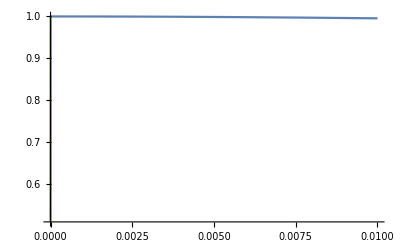

```mathematica
Plot[f[r]/r/.soltemp,{r,0,0.01},PlotRange->All]
```

```mathematica
Table[First@Block[{r1=20000.,r2=10^-10},NDSolve[{Vs2[r,a,{c2,d1}] f[r]-f''[r]/αSch==ene f[r],f[r2]==u0,f'[r2]==1},f,{r,r1,r2},PrecisionGoal->15]],{ene,ee}];
```

```mathematica
(NIntegrate[f[r]^2/.#,{r,10^-10,0.01},MaxRecursion->20]^-0.5 f[r]/.#)&/@%
```

{1732.12                              -10
InterpolatingFunction[{{1. 10   , 20000.}}, <>][r],1732.12                              -10
InterpolatingFunction[{{1. 10   , 20000.}}, <>][r],1732.13                              -10
InterpolatingFunction[{{1. 10   , 20000.}}, <>][r],1732.13                              -10
InterpolatingFunction[{{1. 10   , 20000.}}, <>][r],1732.15                              -10
InterpolatingFunction[{{1. 10   , 20000.}}, <>][r],1732.16                              -10
InterpolatingFunction[{{1. 10   , 20000.}}, <>][r],1732.23                              -10
InterpolatingFunction[{{1. 10   , 20000.}}, <>][r],1732.36                              -10
InterpolatingFunction[{{1. 10   , 20000.}}, <>][r],1732.47                              -10
InterpolatingFunction[{{1. 10   , 20000.}}, <>][r],1733.16                              -10
InterpolatingFunction[{{1. 10   , 20000.}}, <>][r],1734.55                              -10
InterpolatingFunction[{{1. 10   , 20000.}}, <>][r],1735.59                              -10
InterpolatingFunction[{{1. 10   , 20000.}}, <>][r]}

```mathematica
efVs2=%;
```

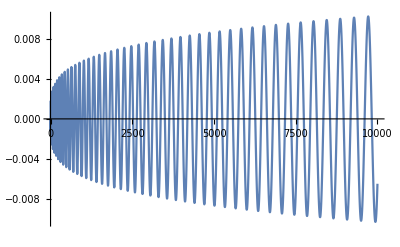

```mathematica
Plot[efVs2[[1]],{r,0,10000}]
```

```mathematica
efVs2[[1]]/(√(4π))δa[r]r/.r->100
```

3.23918753263056×10^-21714721

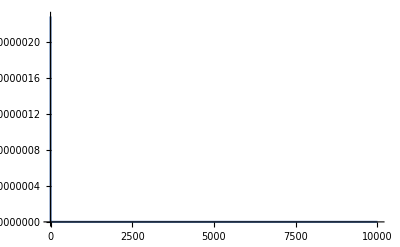

```mathematica
Plot[efVs2[[1]]/(√(4π))δa[r]r,{r,0,10000},PlotRange->All]
```

```mathematica
NIntegrate[efVs2[[#]]/(√(4π)r)δa[r] r^2,{r,0,10000.},MaxRecursion->20]&/@Range@1
```

{0.0000678693}

#### ψ_r Vs_2

```mathematica
IntegrationVs21st=NIntegrate[efVs2[[#]]/(√(4π)r)δa[r] r^2,{r,0,20000.},MaxRecursion->20]&/@Range@Length@ee
IntegrationVs22nd=NIntegrate[efVs2[[#]]/(√(4π)r)Laplacian[δa[r],{r,θ,ϕ},"Spherical"] r^2,{r,0,20000.},MaxRecursion->20]&/@Range@Length@ee
```

NIntegrate::ncvb: 在接近 {r} = {1.1022} 处的 r 中进行 20 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 5.67654×10^-10 和 2.09945×10^-15.

{7.58374,7.57372,6.63779,5.05319,2.83501,1.7641,-0.18293,-0.0429977,-0.0061497,1.00224×10^-6,-5.40749×10^-9,5.67654×10^-10}

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {1.1022} 处的 r 中进行 20 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 1.75804×10^-9 和 4.00445×10^-15.

{-25.0012,-24.9989,-24.6474,-23.3526,-19.4935,-16.2788,-2.65275,0.214054,0.0618744,-0.0000104784,7.64763×10^-9,1.75804×10^-9}

```mathematica
ψrTrueVs2[n_][γ_,η_]:=4π(γ IntegrationVs21st[[n]]+η a^2 IntegrationVs22nd[[n]])
```

```mathematica
DetermineVs2[r0_]:=Module[{REAL,REF,RES,ψr,ERROR,REFRANGE={1,2}},
(*Print[r0];*)
(*REAL=NLimit[efV[[#]]/(√(4π)r),r->r0,WorkingPrecision->30]&/@Range@20;*)
REF=(Limit[RS[ee[[#]],r]/(√(4π)),r->r0]&/@REFRANGE);
RES=FindRoot[Thread[ψrTrueVs2[#][γ,η]&/@REFRANGE==REF],{{γ,0,1},{η,0,1}},AccuracyGoal->10,MaxIterations->200,WorkingPrecision->30];
(*ψr=ψrTrue[#][γ,η]/.RES&/@Range@20;
ERROR=Abs[(ψr-REAL)/REAL];*)
(*Print[N[ERROR,6]];*)
{{r0,γ},{r0,η}(*,N[ERROR,6]*)}/.RES
]
```

```mathematica
N@(Limit[RS[ee[[#]],r]/(√(4π)),r->0]&/@{1,2})
```

{0.0165569090208428+0.00295152098934274 ⅈ,-0.212921+0.210017 ⅈ}

```mathematica
{ IntegrationVs21st[[1]],a^2 IntegrationVs22nd[[1]]}
```

{0.0000678693,-1.03294×10^-6}

```mathematica
FindRoot[{4π(γ IntegrationVs21st[[1]]+η a^2 IntegrationVs22nd[[1]])==0.01655690902084281216601652560258834851`15.653559774527023+0.0029515209893427405511890448223658802`15.653559774527023 ⅈ,4π(γ IntegrationVs21st[[2]]+η a^2 IntegrationVs22nd[[2]])==-0.2129211967419823+0.2100173399458991 ⅈ},{γ,0+0I,1+1I},{η,0+0I,1+1I}]
```

{γ→1.19863×10^7-1.01059×10^7 ⅈ,η→7.87558×10^8-6.64007×10^8 ⅈ}

```mathematica
4π(γ IntegrationVs21st[[1]]+η a^2 IntegrationVs22nd[[1]])/.%140
```

0.0165569+0.00295152 ⅈ

```mathematica
Solve[{4π(γ IntegrationVs21st[[1]]+η a^2 IntegrationVs22nd[[1]])==0.01655690902084281216601652560258834851`15.653559774527023+0.0029515209893427405511890448223658802`15.653559774527023 ⅈ,4π(γ IntegrationVs21st[[2]]+η a^2 IntegrationVs22nd[[2]])==-0.2129211967419823+0.2100173399458991 ⅈ},{γ,η}]
```

{{γ→35.9341-32.4245 ⅈ,η→2361.05-2130.46 ⅈ}}

```mathematica
FindRoot[Thread[ψrTrueVs2[#][γ,η]&/@{1,2}==%134],{{γ,0,I},{η,0,I}}]
```

{γ→35.9341-32.4245 ⅈ,η→2361.05-2130.46 ⅈ}

```mathematica
DetermineVs2[0]
```

FindRoot::precw: 参数函数的精度 ({4 π (7.58374 γ-25.0012 η)==(ⅇ^(2500 √2 π) Gamma[1-5000 ⅈ √2])/(5000 √(2 π)),4 π (7.57372 γ-24.9989 η)==(ⅇ^(5 √5 π) Gamma[1-10 ⅈ √5])/(10 √(5 π))}) 小于 WorkingPrecision (30.).

{{0,1.95891655242100421947407295249-1.76761050459653603240166887109 ⅈ},{0,0.594154418405560418043493387449-0.536186774052367360007668801753 ⅈ}}

```mathematica
Module[{γη},
γlVs2={};ηlVs2={};
Monitor[Table[
γη=DetermineVs2[r0];
AppendTo[γlVs2,γη[[1]]];
AppendTo[ηlVs2,γη[[2]]];
,{r0,0,1,0.001}],Row[{ProgressIndicator[r0,{0,1}],100 r0/1"%"}]]];
```

FindRoot::precw: 参数函数的精度 ({4 π (7.58374 γ-25.0012 η)==0.0165569+0.00295152 ⅈ,4 π (7.57372 γ-24.9989 η)==-0.212921+0.210017 ⅈ}) 小于 WorkingPrecision (30.).

FindRoot::precw: 参数函数的精度 ({4 π (7.58374 γ-25.0012 η)==0.0165404+0.00294857 ⅈ,4 π (7.57372 γ-24.9989 η)==-0.212708+0.209807 ⅈ}) 小于 WorkingPrecision (30.).

FindRoot::precw: 参数函数的精度 ({4 π (7.58374 γ-25.0012 η)==0.0165238+0.00294562 ⅈ,4 π (7.57372 γ-24.9989 η)==-0.212496+0.209598 ⅈ}) 小于 WorkingPrecision (30.).

General::stop: 在本次计算中，FindRoot::precw 的进一步输出将被抑制.

```mathematica
γrVs2=Interpolation[γlVs2]
ηrVs2=Interpolation[ηlVs2]
```

InterpolatingFunction[{{0., 1.}}, <>]

InterpolatingFunction[{{0., 1.}}, <>]

```mathematica
ψrfunVs2[r_][n_]:=4π(γrVs2[r] IntegrationVs21st[[n]]+ηrVs2[r] a^2 IntegrationVs22nd[[n]])
```

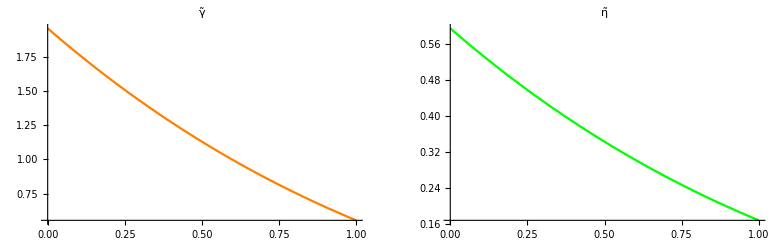

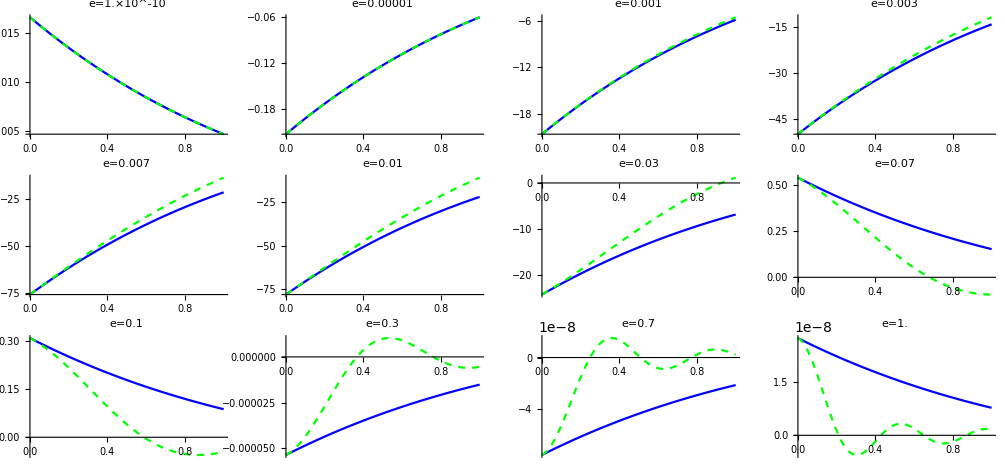

```mathematica
GraphicsGrid@{{Plot[Re@γrVs2[r],{r,0,1},ImageSize->Medium,PlotStyle->Orange,PlotLabel->"γ̃"],Plot[Re@ηrVs2[r],{r,0,1},ImageSize->Medium,PlotStyle->Green,PlotLabel->"η̃"]}}
GraphicsGrid@Partition[Table[Plot[Evaluate@Re@{ψrfunVs2[r][n],(ψrfunVs2[0.005][n])/(RS[ee[[n]],0.005]/Sqrt[4 π])RS[ee[[n]],r]/(√(4π))},{r,0,1},PlotStyle->{Blue,{Green,Dashed}},PlotLabel->"e="<>ToString[N[ee[[n]]],TraditionalForm],ImageSize->230],{n,1,Length@ee}],4]
```